## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="u-d";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

{{3,3,3,1,3,3,3,1,3,3,3},{3,3,1,3,3,1,3,3,3,1,3,3},{3,3,1,3,3,3,1,3,3,1,3,3},{3,3,1,3,3,1,3,1,3,3,1,3,3}}

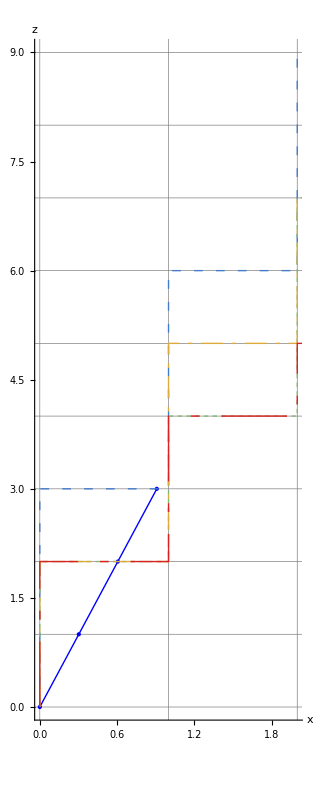

```mathematica
v1[v3_]:=v3*0.303;
PathToLinks[sidelink_] :=(
ULinkslist={};
AppendTo[ULinkslist,{0,0,0}];
Do[
linki = sidelink[[i]];
If[linki==1,
AppendTo[ULinkslist, {ULinkslist[[i]][[1]]+1,ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]}]];
If[linki==3,
AppendTo[ULinkslist, {ULinkslist[[i]][[1]],ULinkslist[[i]][[2]],ULinkslist[[i]][[3]]+1}]];
,{i,Length[sidelink]}];
Return[ULinkslist];
)
vvector = {};
Do[
AppendTo[vvector, {v1[v3],0,v3}],{v3, 0, 3}];

latticevvector = {};

vlinks = Union[MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==9&]
Do[AppendTo[latticevvector,PathToLinks[vlinksv3[[variousv]]]]
,{variousv, Length[vlinksv3]}]
Graphics[{Blue,PointSize[Large],Point[vvector[[All,{1,3}]]],Blue,Thick,Line[vvector[[All,{1,3}]]],Table[{ColorData["Rainbow"][i/Length[latticevvector]],Dashing[Switch[i,1,{0.02,0.03},(*Fine dashed line*)2,{0.01,0.01},(*Coarse dashed line*)3,{0.05,0.02,0.01,0.02},(*Dash-dot pattern*)4,{0.15,0.05,0.02,0.05},(*Dash-dash-dot pattern*)5,{0.2,0.05},(*Long dashed line*)6,{0.02,0.02,0.02,0.1},(*Two small dashes and a gap*)7,{0.05,0.05,0.01,0.05,0.01},(*Complex dash-dot-dash pattern*)_,{0.1,0.05}                    (*Default pattern*)]],Line[latticevvector[[i]][[All,{1,3}]]]},{i,Length[latticevvector]}]},Axes->True,AxesLabel->{"x","z"},GridLines->{Range[-6,6],Range[-14,14]},GridLinesStyle->Directive[Gray], PlotRange->{{0,2},{0,9}}]
```

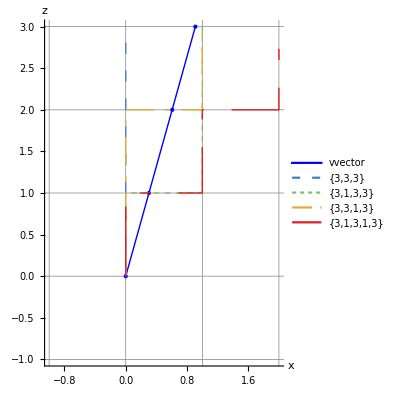

```mathematica
(*1. Define the styles first so the plot and legend match perfectly*)lineStyles=Table[Directive[ColorData["Rainbow"][i/Length[latticevvector]],Dashing[Switch[i,1,{0.02,0.03},2,{0.01,0.01},3,{0.05,0.02,0.01,0.02},4,{0.15,0.05,0.02,0.05},5,{0.2,0.05},6,{0.02,0.02,0.02,0.1},7,{0.05,0.05,0.01,0.05,0.01},_,{0.1,0.05}]]],{i,Length[latticevvector]}];

(*2. Generate the Legended plot*)
Legended[Graphics[{Blue,PointSize[Large],Point[vvector[[All,{1,3}]]],Blue,Thick,Line[vvector[[All,{1,3}]]],(*Use the styles we defined above*)Table[{lineStyles[[i]],Line[latticevvector[[i]][[All,{1,3}]]]},{i,Length[latticevvector]}]},Axes->True,AxesLabel->{"x","z"},GridLines->{Range[-6,6],Range[-14,14]},GridLinesStyle->Directive[Gray],PlotRange->{{-1,2},{-1,3}}],Placed[LineLegend[(*Pass the thick blue directive,followed by our custom dashed styles*)Prepend[lineStyles,Directive[Blue,Thick]],(*Legend Labels from vlinksv3*)Prepend[vlinksv3,"vvector"]],Right]]
```

v links = {{3,3,3},{3,1,3,3},{3,3,1,3},{3,1,3,1,3}}

= 3

✓ Same  with different sidelink are averaged

= {0.909,-0.091,-1.091}

= {⟨-0.0128(54)⟩_(2902J), ⟨0.0224(54)⟩_(2902J), ⟨0.0490(50)⟩_(2902J)}

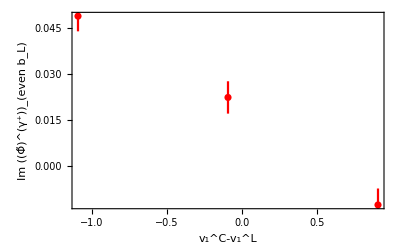

InterpolatingFunction[…]

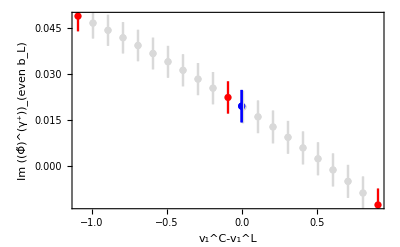

Interpolation for   --->  ⟨0.0195(54)⟩_(2902J)

```mathematica
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->{2,1},sideLink->vlinksv3[[i]],numberFilter->Im}],data];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->{2,1},sideLink->vlinksv3[[i]],numberFilter->Re}],data];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1},sideLink->vlinksv3[[i]],numberFilter->Im}],data];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1},sideLink->vlinksv3[[i]],numberFilter->Re}],data];
blPgPlusIm = (blPg1Re+blPg8Im)/Sqrt[2];
blNgPlusIm = (blNg1Re+blNg8Im)/Sqrt[2];
blEvengPlusIm = blPgPlusIm;
AppendTo[vvectoranddata,{v1data,blEvengPlusIm[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}]
Print["v links = ",vlinksv3]
Print[" = ",v1data[[3]]]
Print["✓ Same  with different sidelink are averaged"];
Print[" = ",v1dataforInterpolation]
Print[" = ",dataforInterpolation//OutputForm]
plotforinterpolation = Transpose[{v1dataforInterpolation,dataforInterpolation}];
plotbeforinterpol= ErrorListPlot[MakeErrBars[plotforinterpolation], Frame->True ,PlotRangePadding->Scaled[.3],FrameLabel->{Style[,Large],Style[,Large]},PlotStyle->Red]
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2]
interpol0 = {{0,fninterpol[0]}};
Show[ErrorListPlot[Table[MakeErrBars[{{x,fninterpol[x]}}],{x, Min[v1dataforInterpolation],Max[v1dataforInterpolation],0.1}],PlotStyle->LightGray, Frame->True ,PlotRangePadding->Scaled[.3],FrameLabel->{Style[,Large],Style[,Large]}],ErrorListPlot[MakeErrBars[interpol0],PlotStyle->Blue],plotbeforinterpol]
Print["Interpolation for   --->  ",fninterpol[0]//OutputForm]
```

```mathematica
AllLinkPathList = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Re}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
(*Do[Print[i,") ",PathToShift[DistinctLinkPaths[[i+1]],3],"<------->",DistinctLinkPaths[[i+1]], "<------->", MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates],{i,CountDistinct[AllLinkPathList]-1}]*)
Print["linkPaths -> {} are skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]], MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates}],{i,CountDistinct[AllLinkPathList]-1}]
(*bveclinkPathsideNumLIST//MatrixForm*)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&& #[[2]]!={1,2,1,1,2,1,2,1,1,2}&];
Print["linkPath -> {1,2,1,1,2,1,2,1,1,2} is skipped"];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&& #[[1,1]]!=-7 &];
Print["linkPath corresponding to b1 = -7 is skipped"];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1listall= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
b1list = Select[b1listall,#!=-7&];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 7225

Total No. Distinct linkPath = 87

linkPaths -> {} are skipped

linkPath -> {1,2,1,1,2,1,2,1,1,2} is skipped

linkPath corresponding to b1 = -7 is skipped

b2 = {-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

b1 = {-8,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,8}

({0,1,0} | {2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,2,0} | {2,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,3,0} | {2,2,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,4,0} | {2,2,2,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,5,0} | {2,2,2,2,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,6,0} | {2,2,2,2,2,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,7,0} | {2,2,2,2,2,2,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-1,0} | {-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-2,0} | {-2,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-3,0} | {-2,-2,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-4,0} | {-2,-2,-2,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-5,0} | {-2,-2,-2,-2,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-6,0} | {-2,-2,-2,-2,-2,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30})

({1,1,0} | {2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,2,0} | {2,1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{3,3,0} | {2,1,2,1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,4,0} | {2,1,2,1,2,1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{1,1,0} | {1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,2,0} | {1,2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{3,3,0} | {1,2,1,2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,4,0} | {1,2,1,2,1,2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{1,2,0} | {2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,4,0} | {2,1,2,2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{3,6,0} | {2,1,2,2,1,2,2,1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,1,0} | {1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,2,0} | {1,2,1,1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{6,3,0} | {1,2,1,1,2,1,1,2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,1,0} | {1,1,2,1,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{1,-1,0} | {-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,-2,0} | {-2,1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{3,-3,0} | {-2,1,-2,1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{1,-1,0} | {1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,-2,0} | {1,-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{3,-3,0} | {1,-2,1,-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{1,-2,0} | {-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,-4,0} | {-2,1,-2,-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{2,-1,0} | {1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,-2,0} | {1,-2,1,1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{4,-1,0} | {1,1,-2,1,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30})

({-1,1,0} | {2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,2,0} | {2,-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-3,3,0} | {2,-1,2,-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-1,1,0} | {-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,2,0} | {-1,2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-3,3,0} | {-1,2,-1,2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-1,2,0} | {2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,4,0} | {2,-1,2,2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,1,0} | {-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,2,0} | {-1,2,-1,-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,1,0} | {-1,-1,2,-1,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-1,-1,0} | {-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,-2,0} | {-2,-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-1,-1,0} | {-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,-2,0} | {-1,-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-1,-2,0} | {-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-2,-1,0} | {-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-4,-1,0} | {-1,-1,-2,-1,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1} | {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30})

14

36

36

✓ Checked: linkPaths corresponding to   are found

```mathematica
MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Im}],{sideNum}]//Union
```

{{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30}}

```mathematica
(*PlateauRange={10,11,12,13,14};
Print["\n PlateauRange = ", PlateauRange, "\n"];
TablePlateauEvengPlusImForb = {};
(*Print["considering only positive b2"];*)
Do[
PlateauEvengPlusIm=0;
count=0;
(*If[ bveclinkPathsideNumLISTforbL0[[i,1]][[2]]<0,Continue[]];(*considering only positive b2*)
If[ bveclinkPathsideNumLISTforbL0[[i,1]][[2]]>4,Continue[]];*)
Do[
(*If[ bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]]== 0,Continue[]];*)
bl0g8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbL0[[i,2]],sideNum-> bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]],numberFilter->Im}],{sideExtent,data}];
bl0g1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bveclinkPathsideNumLISTforbL0[[i,2]],sideNum-> bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]],numberFilter->Re}],{sideExtent,data}];
etaList = bl0g8Im[[All,1]];
If[ Round[(Length[etaList]-1)]< Max[PlateauRange],Continue[]];
bl0gPlusIm = (bl0g1Re[[All, 2]]+bl0g8Im[[All, 2]])/Sqrt[2];
PlotblEvengPlusIm=Transpose[{etaList,bl0gPlusIm}];
(*PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-4+n),{n,0,4}];
Print["Averaging  values: ",PlateauRange];*)
     PlateauPluseta = 0;
(*PlateauMinuseta = 0;*) (* data has onlu positive sideExtent*)
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
(*blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];*)

PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
(*PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];*)

,{PlateauEta, PlateauRange}];
(*PlateauEvengPlusImsideNumj = (-PlateauMinuseta+PlateauPluseta)/2;*)
PlateauEvengPlusImsideNumj = PlateauPluseta;
(*Print[bveclinkPathsideNumLISTforbL0[[i,1]]," ",bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]]," ",PlateauEvengPlusImsideNumj//OutputForm];*)
(*PlateauEvengPlusIm += PlateauEvengPlusImsideNumj/(Length[bveclinkPathsideNumLISTforbL0[[i,3]]]); (*-1 because we are skipping sideNum 0*)*)
PlateauEvengPlusIm += PlateauEvengPlusImsideNumj;
count += 1;
,{sideNumj, Length[bveclinkPathsideNumLISTforbL0[[i,3]]]}];
If[ count==0,Continue[]];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbL0[[i,1]],PlateauEvengPlusIm[[1]]/count}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

Do[
PlateauEvengPlusIm=0;
count=0;
(*If[ bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]]<0,Continue[]];(*considering only positive b2*)
If[ bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]]>4,Continue[]];*)
Do[
(*noErrorvT=True;
(*check v1*)
Do[If[((PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]],numberFilter->Re}],sideLink][[num]],3][[2]])+(PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLnegative[[i,3]][[sideNumj]],numberFilter->Re}],sideLink][[num]],3][[2]]))=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noErrorvT=False;]
,{num,Length[Union[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]]}],sideExtent]]]}];*)
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]],numberFilter->Im}],{sideExtent,data}];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]],numberFilter->Re}],{sideExtent,data}];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLnegative[[i,3]][[sideNumj]],numberFilter->Im}],{sideExtent,data}];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLnegative[[i,3]][[sideNumj]],numberFilter->Re}],{sideExtent,data}];
etaList = blPg8Im[[All,1]];
If[ Round[(Length[etaList]-1)]< Max[PlateauRange],Continue[]];
blPgPlusIm = (blPg1Re[[All, 2]]+blPg8Im[[All, 2]])/Sqrt[2];
blNgPlusIm = (blNg1Re[[All, 2]]+blNg8Im[[All, 2]])/Sqrt[2];
blEvengPlusIm = (blPgPlusIm+blNgPlusIm)/2;
PlotblEvengPlusIm=Transpose[{etaList,blEvengPlusIm}];
(*PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-4+n),{n,0,4}];*)
     PlateauPluseta = 0;
(*PlateauMinuseta = 0;*) (* data has onlu positive sideExtent*)
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
(*blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];*)

PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
(*PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];*)

,{PlateauEta, PlateauRange}];
(*PlateauEvengPlusImsideNumj = (-PlateauMinuseta+PlateauPluseta)/2;*)
PlateauEvengPlusImsideNumj = PlateauPluseta;
(*PlateauEvengPlusIm += PlateauEvengPlusImsideNumj/(Length[bveclinkPathsideNumLISTforbLpositive[[i,3]]]-1);(*-1 because we are skipping sideNum 0*)*)
PlateauEvengPlusIm += PlateauEvengPlusImsideNumj;
count += 1;
,{sideNumj, Length[bveclinkPathsideNumLISTforbLpositive[[i,3]]]}];
If[ count==0,Continue[]];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLpositive[[i,1]],PlateauEvengPlusIm[[1]]/count}];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLnegative[[i,1]],PlateauEvengPlusIm[[1]]/count}];
  ,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];*)
```

```mathematica
(*Print[TablePlateauEvengPlusImForb//OutputForm]*)
```

```mathematica
(*groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["\n PlateauRange = ", PlateauRange, "\n"];
Print["✓ Same  with different linkPath are averaged\n"];
Print["     -even component of imaginary part of  correlator"];
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print[PlotbL];
datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```